```mathematica
(* min z=4x1-3x2+5
 x1+4x2<=40
-2x1+2x2>=12
-3x1- x2<=15 *)
```

```mathematica
g1[x1_,x2_]:=x1+4x2;
g2[x1_,x2_]:=-2x1+2x2;
g3[x1_,x2_]:=-3x1-x2;
b1=40;
b2=12;
b3=15;
```

```mathematica
g1[x1_]=x2/.Solve[g1[x1,x2]==b1,{x2}][[1,1]];
g2[x1_]=x2/.Solve[g2[x1,x2]==b2,{x2}][[1,1]];
g3[x1_]=x2/.Solve[g3[x1,x2]==b3,{x2}][[1,1]];
```

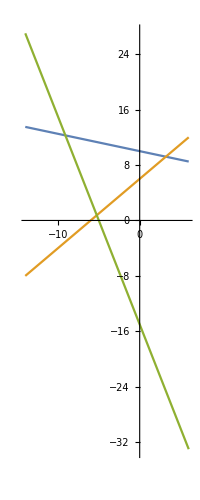

```mathematica
Plot[{g1[x],g2[x],g3[x]},{x,-14,6},AspectRatio->Automatic]
```

```mathematica
Plot[{g1[x],g2[x],g3[x]},{x,-14,6},AspectRatio->1,PlotRange->{-5,15}]
```

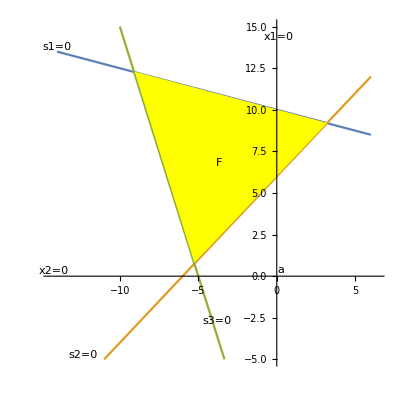

```mathematica
a0={"u1","u2","u3","u4","s1","s2","s3","z","rhs"};
a1={1,-1,4,-4,1,0,0,0,40};
a2={2,-2,-2,2,0,1,0,0,-12};
a3={-3,3,-1,1,0,0,1,0,15};
aobj={-4,4,3,-3,0,0,0,1,5};
a={a0,a1,a2,a3,aobj};
Print["a = ", MatrixForm[a]]
```

a = (u1 | u2 | u3 | u4 | s1 | s2 | s3 | z | rhs
1 | -1 | 4 | -4 | 1 | 0 | 0 | 0 | 40
2 | -2 | -2 | 2 | 0 | 1 | 0 | 0 | -12
-3 | 3 | -1 | 1 | 0 | 0 | 1 | 0 | 15
-4 | 4 | 3 | -3 | 0 | 0 | 0 | 1 | 5)

```mathematica
(* basic solution *)
u1=0;u2=0;u3=0;u4=0;
x1=u1-u2;x2=u3-u4;
s1=40;s2=-12;s3=15;z=5;
Print["x1 = ",x1,"x2 = ",x2,"z = ",z]
```

x1 = 0x2 = 0z = 5

```mathematica
b0=a0;
b1=a1/4;
b2=a2+2b1;
b3=a3+b1;
bobj=aobj-3b1;
b={b0,b1,b2,b3,bobj};
Print["b = ", MatrixForm[b]]
```

b = (u1 | u2 | u3 | u4 | s1 | s2 | s3 | z | rhs
1/4 | -1/4 | 1 | -1 | 1/4 | 0 | 0 | 0 | 10
5/2 | -5/2 | 0 | 0 | 1/2 | 1 | 0 | 0 | 8
-11/4 | 11/4 | 0 | 0 | 1/4 | 0 | 1 | 0 | 25
-19/4 | 19/4 | 0 | 0 | -3/4 | 0 | 0 | 1 | -25)

```mathematica
(* basic solution *)
u1=0;u2=0;u3=10;u4=0;
x1=u1-u2;x2=u3-u4;
s1=0;s2=8;s3=25;z=-25;
Print["x1 = ",x1,"x2 = ",x2,"z = ",z]
```

x1 = 0x2 = 10z = -25